# Classifying NK Networks.

An NK network is a boolean network where n specify the number of nodes or vertexes and k is the number of incoming connections that each vertex has. According to Kauffman, the parameter K defines the stability (or lack of thereof) of the network, where k = 2 is a critical point that approximates the properties of gene regulatory networks. Bellow that (k=1) we have too much regularity (frozen state) and beyond it (K>=3) we have chaos.

## The Problem

The classification problem to solve is, can we find out whenever the evolution of an NK network correspond to k=1 (frozen), k = 2 (criticality) and k=3 (chaos)?

#### Legacy Functions

```mathematica
toBinaryInt[n_,bits_]:=IntegerDigits[n,2,bits]
```

The following code contains snips from and code inspired by https://demonstrations.wolfram.com/BooleanNKNetworks/

```mathematica
ConnectivityMatrix[n_,k_]:=Table[RandomSample[Flatten[Prepend[Table[0,{n-k}],Table[1,{k}]]]],{n}]
```

```mathematica
InitialStates[n_]:=RandomInteger[1,n]
```

```mathematica
PositionsMatrix[conM_]:=Map[Flatten,Position[#,1]&/@conM];
```

Rules

The following functions randomly generates boolean rules of degree K.

```mathematica
randomRule[k_]:=
With[
{
outputs =RandomChoice[{0,1},2^k],
inputs = Flatten[toBinaryInt[#,k]&/@Range[2^{k}],1]
},
AssociationThread[inputs-> outputs]
]
```

```mathematica
randomRule[3]
```

<|{0,0,1}→1,{0,1,0}→1,{0,1,1}→0,{1,0,0}→1,{1,0,1}→0,{1,1,0}→1,{1,1,1}→0,{0,0,0}→1|>

Function that generates a random NK network topology.

```mathematica
randomNetwork[n_,k_]:=
With[
{
rules = RandomChoice[
randomRule[k]&/@Range[n]
,n],
connections = PositionsMatrix[ConnectivityMatrix[n,k]]
},
Association[
{
"Connections"->connections,
"Rules"-> rules
}
]
]
```

For example:

```mathematica
randomNetwork[10,2]
```

<|Connections→{{3,4},{2,5},{1,7},{2,9},{6,9},{1,9},{3,6},{5,9},{8,9},{4,7}},Rules→{<|{0,1}→0,{1,0}→0,{1,1}→1,{0,0}→0|>,<|{0,1}→1,{1,0}→0,{1,1}→1,{0,0}→0|>,<|{0,1}→1,{1,0}→1,{1,1}→0,{0,0}→1|>,<|{0,1}→1,{1,0}→1,{1,1}→0,{0,0}→0|>,<|{0,1}→1,{1,0}→1,{1,1}→0,{0,0}→1|>,<|{0,1}→1,{1,0}→1,{1,1}→0,{0,0}→0|>,<|{0,1}→1,{1,0}→1,{1,1}→0,{0,0}→1|>,<|{0,1}→1,{1,0}→0,{1,1}→1,{0,0}→1|>,<|{0,1}→1,{1,0}→0,{1,1}→1,{0,0}→0|>,<|{0,1}→1,{1,0}→1,{1,1}→0,{0,0}→1|>}|>

Given a network topology, the following function evolves a vector of n vectors.

```mathematica
Remove[evolve]
```

```mathematica
evolve[state_, topo_]:=
Table[
With[
{
inputs = (topo["Connections"])[[i]],
trans = (topo["Rules"])[[i]]
},
trans[state[[inputs]]]
]
,{i,Length@state}]
```

For example:

```mathematica
net = randomNetwork[10,2];
```

```mathematica
evolve[{1,0,0,1,0,1,0,1,0,1},net]
```

{0,0,1,1,0,1,0,1,0,1}

```mathematica
v = ConstantArray[0,10]
```

{0,0,0,0,0,0,0,0,0,0}

An evolution of the system for 10 steps is:

```mathematica
NestList[evolve[#,net]&,v,10]
```

{{0,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,0,0,0,0,0},{0,0,1,1,1,0,0,1,0,1},{1,0,1,1,0,0,0,0,0,1},{0,0,1,1,1,0,0,1,0,1},{1,0,1,1,0,0,0,0,0,1},{0,0,1,1,1,0,0,1,0,1},{1,0,1,1,0,0,0,0,0,1},{0,0,1,1,1,0,0,1,0,1},{1,0,1,1,0,0,0,0,0,1},{0,0,1,1,1,0,0,1,0,1}}

## The Data Sets

The data sets consists of the evolution up time t=10 of 24 vertex nk-Boolean networks for each category of k=1,2,3.

```mathematica
n= 24
```

24

```mathematica
start = ConstantArray[0,n]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

According to Kaufman, k=2 represents a critical point, where the network becomes interesting.

Let’s see how is the evolution of the network.

```mathematica
size = 100;
```

```mathematica
SeedRandom[02042019]
s1 = evolve[start,randomNetwork[n,1]]&/@Range[size];
s2 = evolve[start,randomNetwork[n,2]]&/@Range[size];
s3 = evolve[start,randomNetwork[n,3]]&/@Range[size];
s4 = evolve[start,randomNetwork[n,4]]&/@Range[size];
```

Let’s see if there’s any BDM regularity.

## String BDM.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
D5 = <<"D5.m";
```

Adding missing strings:

```mathematica
D5=Flatten/@Append[D5,{{"000110100111",(5.21946101832149*^-12)}}];
D5=Flatten/@Append[D5,{{"111001011000",(5.21946101832149*^-12)}}];
```

```mathematica
Table[HashStrings[D5[[i,1]]] = -Log[2,D5[[i,2]]],{i,Length@D5}];
```

```mathematica
StringBDM[string_,len_:1]:= 
N@Total[HashStrings[#[[1]]]+Log[2,#[[2]]]&/@Tally[If[TrueQ[StringLength[string]>12],StringPartition[string,12,len],{string}]]]
```

Modified version of String Entropy to be able to setup partition sizes.

```mathematica
StringBDMS[string_,len_:1, dis_:1]:= 
N@Total[HashStrings[#[[1]]]+Log[2,#[[2]]]&/@Tally[
StringPartition[string,len,dis]]
]
```

```mathematica
BinaryBDM[input_,len_:1]:=
With[
{str = StringJoin[ToString/@input]},
StringBDM[str,len]
]
```

## The Sets:

We will include the evolution of a network up to 10 times.

```mathematica
flattenEvo[ str_,net_,t_]:= Flatten@Rest@NestList[evolve[#,net]&,str,t]
```

```mathematica
net = randomNetwork[24,2];
```

```mathematica
BinaryBDM@RandomChoice[{0,1},n*10]
```

7093.27

Let’s see the expected values for these sets.

```mathematica
SeedRandom[02042019]
s1 = flattenEvo[start,randomNetwork[n,1],10]&/@Range[size];
s2 = flattenEvo[start,randomNetwork[n,2],10]&/@Range[size];
s3 = flattenEvo[start,randomNetwork[n,3],10]&/@Range[size];
s4 = flattenEvo[start,randomNetwork[n,4],10]&/@Range[size];
```

```mathematica
Mean[BinaryBDM/@s1]
```

2541.57

```mathematica
Mean[BinaryBDM/@s2]
```

5018.44

```mathematica
Mean[BinaryBDM/@s3]
```

6625.2

```mathematica
Mean[BinaryBDM/@s4]
```

7191.18

Looks like we will be able to separate sets according to the BDM!

The Sets

```mathematica
classes = {1,2,3}
```

{1,2,3}

```mathematica
size = 100;
```

```mathematica
SeedRandom[02042019]
TrainingSample =
 Flatten@Table[
Table[
flattenEvo[
start,
randomNetwork[n,classes[[j]]],
10]->classes[[j]]
,{i,size}]
,{j,Length@classes}];

ValidationSample =
 Flatten@Table[
Table[
 flattenEvo[
start,
randomNetwork[n,classes[[j]]],
10]->classes[[j]]
,{i,size}]
,{j,Length@classes}];

TestSample =
 Flatten@Table[
Table[
 flattenEvo[
start,
randomNetwork[n,classes[[j]]],
10]->classes[[j]]
,{i,size}]
,{j,Length@classes}];
```

The data has the form:

```mathematica
TrainingSample[[1]]
```

{0,0,0,1,1,0,1,1,1,1,0,1,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,1,1,0,1,1,1,1,0,0,1,1,0,0,0,1,0,1,1,1,0,0,0,0,0,1,1,0,1,1,1,1,0,0,1,1,0,0,0,0,0,1,1,1,0,0,0,0,0,1,1,0,1,1,1,1,0,0,1,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,1,0,1,1,1,1,0,0,1,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,1,0,1,1,1,1,0,0,1,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,1,0,1,1,1,1,0,0,1,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,1,0,1,1,1,1,0,0,1,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,1,0,1,1,1,1,0,0,1,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,1,0,1,1,1,1,0,0,1,1,0,0,0,0,0,1,0,1,0,0}→1

```mathematica
Length@TrainingSample[[1,1]]
```

240

Where the object to classify is the evolution to 10 steps of the Boolean network while the class if the $K$ parameter that was used to generate the network.

## Solving the Classification Problem With Neural Networks.

Lets see if a neural network can solve classify the previous set.

```mathematica
nn = NetChain[
{ 
LinearLayer[n*10],Ramp,DropoutLayer[],
LinearLayer[],Ramp,SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",classes}],"Input"-> {n*10}
]
```

NetChain[<>]

```mathematica
SeedRandom[02042019]
net = NetTrain[nn,
TrainingSample, 
ValidationSet->ValidationSample,
TargetDevice->{"GPU",2}]
```

NetChain[<>]

```mathematica
ClassifierMeasurements[net, TestSample, "Accuracy"]
```

0.426667

```mathematica
ClassifierMeasurements[net, TrainingSample, "Accuracy"]
```

1.

```mathematica
nn2 = NetChain[
{ 
LinearLayer[n*10],Ramp,DropoutLayer[],
LinearLayer[],SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",classes}],"Input"-> {n*10}
]
```

NetChain[<>]

```mathematica
SeedRandom[02042019]
net2 = NetTrain[nn2,
TrainingSample, 
ValidationSet->ValidationSample,
TargetDevice->{"GPU",2}]
```

NetChain[<>]

```mathematica
ClassifierMeasurements[net2, TestSample, "Accuracy"]
```

0.43

As expected, the NN is not good at classifying this problem, and the network has enough variance to perfectly fit the set.

```mathematica
ClassifierMeasurements[net, TrainingSample, "Accuracy"]
```

1.

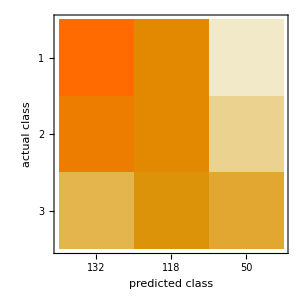

```mathematica
ClassifierMeasurements[net2, TestSample , "ConfusionMatrixPlot"]
```

Looks like most incorrect classifications are assigned to the k=1 class.

Lets see if Mathematica can find a good classifier.

```mathematica
mClass = Classify[TrainingSample]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[mClass, TestSample, "Accuracy"]
```

0.35

```mathematica
ClassifierMeasurements[mClass, TrainingSample, "Accuracy"]
```

0.643333

Using GradientBoostedTrees performed worse, nearly as bad as random classification.

### An Attempt of Using a Prior Information of the Problem.

By construction, we know that the starting strings are of size 24, so how can we use that information to define a better topology for the Neural Network? The one solution that comes to mind is to use convolutional layers of size {24,10} with

```mathematica
TrainingSample2 = ({#[[1]]}->#[[2]])&/@TrainingSample;
ValidationSample2 = ({#[[1]]}->#[[2]])&/@ValidationSample;
TestSample2 = ({#[[1]]}->#[[2]])&/@TestSample;
```

```mathematica
nn3 =  NetChain[{ ConvolutionLayer[10,{24}],Ramp, (* DropoutLayer[], *)
PoolingLayer[{24}, "Function"->Mean],FlattenLayer[], 
LinearLayer[Length@classes],SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",classes}],"Input"-> {1,n*10}];
```

```mathematica
SeedRandom[02042019]
net3 = NetTrain[nn3,TrainingSample2, ValidationSet->ValidationSample2, TargetDevice->{"GPU",2}]
```

NetChain[<>]

```mathematica
ClassifierMeasurements[net3, TestSample2, "Accuracy"]
```

0.316667

At the least we managed to somewhat control overfitting:

```mathematica
ClassifierMeasurements[net3, TrainingSample2, "Accuracy"]
```

0.976667

Predictably, that approach didn’t work.

## Algorithmic Classification

Let’s classify purely by using the BDM of the samples.

```mathematica
BDMTrainingSample = (BinaryBDM[#[[1]]]->#[[2]])&/@TrainingSample;
BDMTestSample = (BinaryBDM[#[[1]]]->#[[2]])&/@TestSample;
```

```mathematica
bdmClass = Classify[BDMTrainingSample, Method->"NearestNeighbors"]
```

ClassifierFunction[…]

Let us see the accuracy of this classifier:

```mathematica
ClassifierMeasurements[bdmClass , BDMTestSample , "Accuracy"]
```

0.7

70% by means of nearest neighbors based on its BDM value is much better than 46%. But, can we do better?

Let’s see the confusion Matrix:

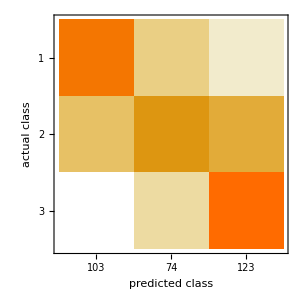

```mathematica
ClassifierMeasurements[bdmClass , BDMTestSample , "ConfusionMatrixPlot"]
```

The class 2, aka the rich one, is the hardest to classify. And most erroneous predictions went to the k=3 case. However, unlike the tested traditional methods,

```mathematica
ClassifierMeasurements[bdmClass , BDMTrainingSample , "Accuracy"]
```

0.71

Boosting the classifier by using both data points.

Let’s combine the data points.

```mathematica
combTrainingSample = (Catenate[{#[[1]],{BinaryBDM[#[[1]]]}}]->#[[2]])&/@TrainingSample;
combValidationSample = (Catenate[{#[[1]],{BinaryBDM[#[[1]]]}}]->#[[2]])&/@ValidationSample;
combTestSample = (Catenate[{#[[1]],{BinaryBDM[#[[1]]]}}]->#[[2]])&/@TestSample;
```

```mathematica
combClass = Classify[combTrainingSample ]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[combClass , combTestSample, "Accuracy"]
```

0.696667

70%, the small difference is not significant.

Let’s try a simple Neural Network.

```mathematica
nn2 = NetChain[
{ 
LinearLayer[n*10+1],Ramp,DropoutLayer[],
LinearLayer[],Ramp,SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",{1,2,3}}],"Input"-> {n*10+1}
]
```

NetChain[<>]

```mathematica
SeedRandom[02042019]
net2 = NetTrain[nn2,combTrainingSample, ValidationSet->combValidationSample]
```

NetChain[<>]

NetChain[<>]

```mathematica
ClassifierMeasurements[net2, combTestSample, "Accuracy"]
```

0.326667

Performance dropped significantly to random classification. I did not expected this result. But help us to show that the used topology has no real way to discern on the useful information for the classification.

```mathematica
ClassifierMeasurements[net2, combTrainingSample, "Accuracy"]
```

0.326667

The Model

The first task is to define the proper model. For this problem, a class is an integer that defines the number of interactions between the nodes of the networks. Follows that a class is composed of all possible interactions of degree k.

In other words, the model is composed of the sets of adjacency matrices of the interactions between the vertices of the network corresponding to the evolution of the model and the . This is of course a really big set. But the complexity of these matrices,

The main challenge we have with algorithmic classification is that NW networks is that mutations aren’t local, therefore we can expect that the the block partition approach used by the Cellular automaton case will yield worse results. Also, doing conditional algorithmic complexity over 2^24 strings in order to get over the block size limitation (for this case) is too costly.

Now, from the previous experiment, is clear that BDM works on some capacity, but that is with the universal distribution. I’m not confident that algorithmic  classification restricted to the set of rules will work nearly as well.

As consequence of the previous points, we have that classification by BDM weights is an instance of algorithmic classification given the following:

The real centers are the sets of all possible algorithmic relations, including the adjacency matrix and related binary operations, related to k=3. Therefore, the expected complexity of specifying a member of each class increases in function of this value (k).

For instance, the number of possible boolean operations of degree k is 2^(2^k) and the number of possible adjacency matrices is n\times Comb(n,k) (for row of each matrix, we must choose k incoming edges out of n possible nodes) . Follows that the total number of possible network topologies is n^2 \times 2^(2^k) \times  Comb(n,k)  and the expected number of bits required to specify a member of this set is Log(n^2 \times 2^(2^k) \times  Comb(n,k)).

Therefore, the expected algorithmic complexity of the members of  each class increases with k and n and we can do a coarse algorithmic classification instance according to this idea.

```mathematica
model = AssociationMap[0&, classes]
```

<|1→0,2→0,3→0|>

Training the model:

```mathematica
ChooseDat[data_, dig_]:=Select[data, (#[[2]]==dig)&]
```

```mathematica
Mean@Keys@ChooseDat[BDMTestSample,1]
```

2671.46

```mathematica
Table[
With[
{cls=classes[[i]]}
,model[cls]= Mean@Keys@ChooseDat[BDMTestSample,cls]
]
,{i,Length@classes}
]
```

{2671.46,4937.35,6837.64}

And we classify a sample with respect to which BDM is the closest to it.

```mathematica
Remove[pred]
```

```mathematica
pred[m_,x_]:= MinimalBy[Keys@m, Abs[m[#]-x]&][[1]]
```

```mathematica
right = 0;
wrong = List[]
Table[
If[
pred[
model, BDMTestSample[[i]][[1]]
]== BDMTestSample[[i]][[2]],
right = right +1,
wrong=Append[wrong,BDMTestSample[[i]]]
]
,{i,Length[BDMTestSample]}];
```

{}

And the accuracy is:

```mathematica
N@right/Length[BDMTestSample]
```

0.713333

On the test set.

```mathematica
right = 0;
wrong2 = List[]
Table[
If[
pred[
model, BDMTrainingSample[[i]][[1]]
]== BDMTrainingSample[[i]][[2]],
right = right +1,
wrong2=Append[wrong2,BDMTrainingSample[[i]]]
]
,{i,Length[BDMTrainingSample]}];
```

{}

```mathematica
N@right/Length[BDMTrainingSample]
```

0.7

71 % for which is almost the same as nearest neighbors!

## Entropy-based Classification

For completeness sake, we will try to see how entropy-based algorithmic information measure does in this classification task.

```mathematica
EntropyTrainingSample = (Entropy[#[[1]]]->#[[2]])&/@TrainingSample;
EntropyTestSample = (Entropy[#[[1]]]->#[[2]])&/@TestSample;
```

```mathematica
entClass = Classify[EntropyTrainingSample ]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[entClass, EntropyTestSample , "Accuracy"]
```

0.376667

Barely above random choice.

```mathematica
ClassifierMeasurements[entClass, EntropyTrainingSample , "Accuracy"]
```

0.463333